(-Sin[t]+Sin[1.5 t])/(Cos[t]-Cos[1.5 t])

-(Sin[0.75 t]+Sin[t])/(Cos[0.75 t]+Cos[t])

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

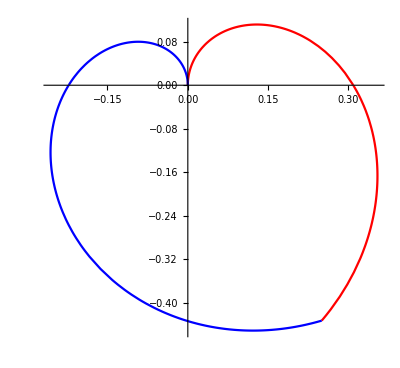

```mathematica
ClearAll["Global`*"]
Xa[a_,t_]:=(a^2*Cos[t]-a*Sin[t])/(1+a^2);
Ya[a_,t_]:=(Sin[t]-a*Cos[t])/(1+a^2);
Aorange[t_]:=(Sin[1.5t]-Sin[t])/(Cos[1.5t]-Cos[t]);
Ablue[t_]:=(Sin[0.75t+Pi]-Sin[t])/(Cos[0.75t+Pi]-Cos[t]);

Print[FullSimplify[(Xa[Aorange[t],t])/(Ya[Aorange[t],t]), 4Pi/3<t<2 Pi]];
Print[FullSimplify[(Xa[Ablue[t],t])/(Ya[Ablue[t],t]), 0<t<4Pi/3]];

(*FullSimplify[Reduce[{x==Xa[Aorange[t],t],y==Ya[Aorange[t],t]},t]]*)

plot1=ParametricPlot[{Xa[Aorange[t],t],Ya[Aorange[t],t]},{t,4Pi/3,2 Pi},PlotRange->All,PlotStyle->Red];
plot2=ParametricPlot[{Xa[Ablue[t],t],Ya[Ablue[t],t]},{t,0,4Pi/3},PlotRange->All,PlotStyle->Blue];
parametricFunc[t_,x_,y_]:={x,y}/.(Solve[x^2+y^2==y*Sin[1.5t]+x*Cos[1.5t]&&x^2+y^2==y*Sin[t]+x*Cos[t],{x,y}]);
plot3=ParametricPlot[parametricFunc[t,x,y],{t,4Pi/3,2 Pi},PlotRange->All,PlotStyle->Black];
Show[plot1,plot2]
```